```mathematica
DateString[]
<<SymbolicComputing`
$Version
$SCVersion
```

Thu 1 Jun 2023 11:04:12

13.2.0 for Microsoft Windows (64-bit) (November 18, 2022)

6.0.2 (June 28, 2021)

## Lecture 20 by Chi-Ok Hwang

### Numerical solution of (Partial) Differential Equations

{{y[x]→InterpolatingFunction[{{0., 10.}}, <>][x]}}

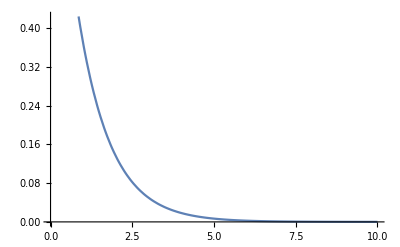

```mathematica
SCNDSolve[{y'[x]+y[x]==0,y[0]==1},y[x],{x,0,10},Rule->True]
Plot[y[x]/.%,{x,0,10}]
```

{{y[x]→InterpolatingFunction[{{0., 10.}}, <>][x]}}

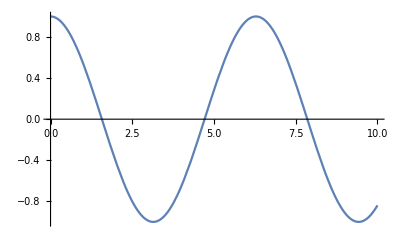

```mathematica
SCNDSolve[ÿ+y==0,{y[0]==1,ẏ[0]==0},y[x],{x,0,10},Rule->True]
Plot[y[x]/.%,{x,0,10}]
```

### Further Examples

{{f[x]→InterpolatingFunction[{{0., 3.14159}}, <>][x],g[x]→InterpolatingFunction[{{0., 3.14159}}, <>][x]}}

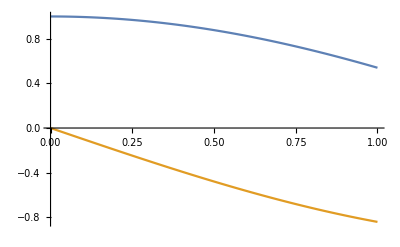

```mathematica
SCNDSolveCoupled[{f'[x]== g[x],g'[x]==-f[x]},{f[0]==1,g[0]==0},{f[x],g[x]},{x,0,π},Rule->True]
Plot[Evaluate[{f[x],g[x]}/.%],{x,0,1}]
```

{{f[x]→InterpolatingFunction[{{0., 1.}}, <>][x],g[x]→InterpolatingFunction[{{0., 1.}}, <>][x]}}

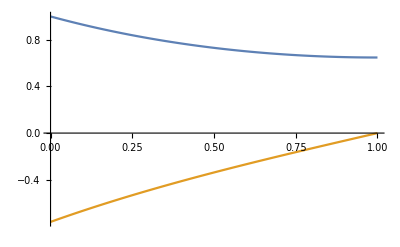

```mathematica
SCNDSolveCoupled[{f'==g,g'== f},{f[0]==1,g[1]==0},{f[x],g[x]},{x,0,1},Rule->True]
Plot[Evaluate[{f[x],g[x]}/.%],{x,0,1}]
```

```mathematica
SCNDSolveValue[{y'[x]+y[x]==0,y[0]==1},y,{x,0,10}]
Plot[%[x],{x,0,10}]
```

InterpolatingFunction[{{0., 10.}}, <>]

-Graphics-

```mathematica
SCNDSolveValue[ÿ+y==0,{y[0]==1,ẏ[0]==0},y,{x,0,10}]
Plot[%[x],{x,0,10}]
```

InterpolatingFunction[{{0., 10.}}, <>]

-Graphics-